```mathematica
img=EdgeDetect[-Graphics-]
```

-Graphics-

```mathematica
lines=ImageLines[img];
```

```mathematica
HighlightImage[img,lines]
```

-Graphics-

```mathematica
EdgeDetect[-Graphics-]
```

-Graphics-

```mathematica
g=Binarize@GradientFilter[-Graphics-,5]//ColorNegate
```

-Graphics-

```mathematica
WatershedComponents[g,Method->{"MinimumSaliency",0.8}]//Colorize
```

-Graphics-

```mathematica
orig = EntityValue[Entity["Lake", "GreatSaltLake::yw8cf"], "Image"];
img = RegionBinarize[orig, -Graphics-, 1/5];
GraphicsRow[{orig, img}]
```

-Graphics-

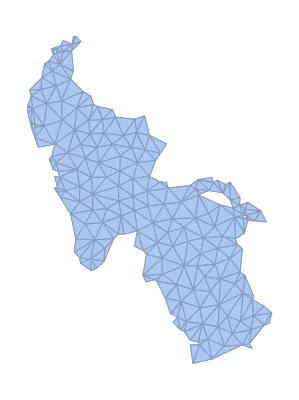

```mathematica
TriangulateMesh[ImageMesh[img]]
```

```mathematica
ImageSubtract[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
RegionBinarize[-Graphics-,-Graphics-,1/5]
```

-Graphics-

```mathematica
(* try again with some dots on the original figure *)
new=ImageResize[-Graphics-,{1580,1358}];
imgm=ColorNegate@RegionBinarize[-Graphics-,-Graphics-,0.1]
```

-Graphics-

```mathematica
delSmall =DeleteSmallComponents[-Graphics-,Method->"Mean"]
```

-Graphics-

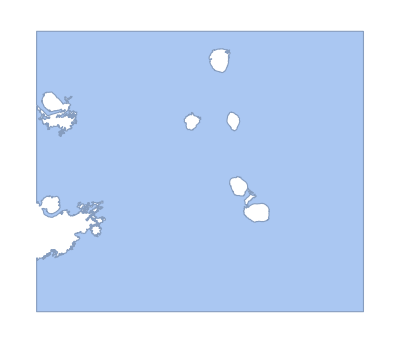

```mathematica
dm=ImageMesh[delSmall]
```

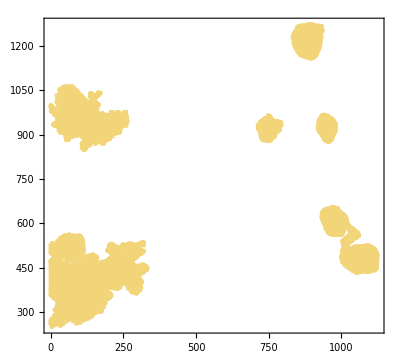

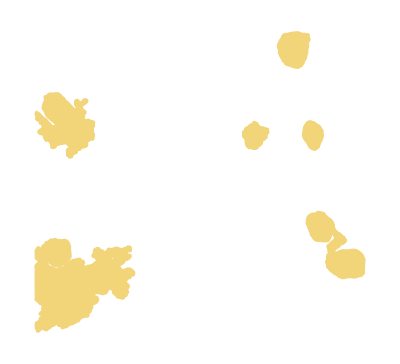

```mathematica
MeshCellCount[%]
```

{6036,6052}

```mathematica
{pts,lines}={MeshCoordinates[dm],MeshCells[dm,1]};
```

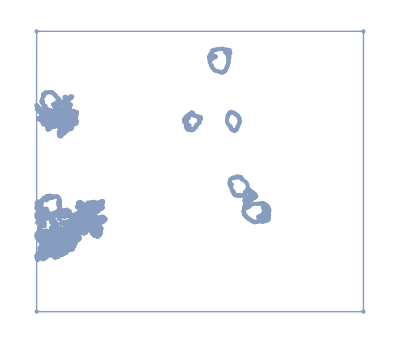

```mathematica
MeshRegion[pts,lines]
```

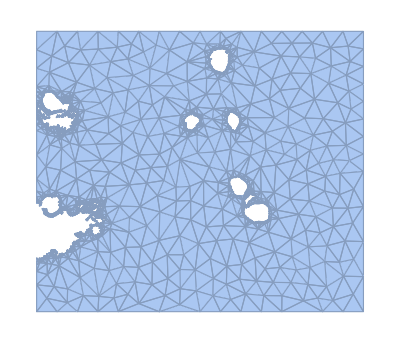

```mathematica
trian=TriangulateMesh[dm]
```

```mathematica
Export["triangulate_mesh.stl",trian, "STL"]
```

triangulate_mesh.stl

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["triangulate_mesh.stl"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["triangulate_mesh"]]]
```

```mathematica
Export["triangulate_mesh.stl",trian, "STL"]
```

triangulate_mesh.stl

```mathematica
imgmn=DeleteSmallComponents[RegionBinarize[-Graphics-,-Graphics-,0.1]]
```

-Graphics-

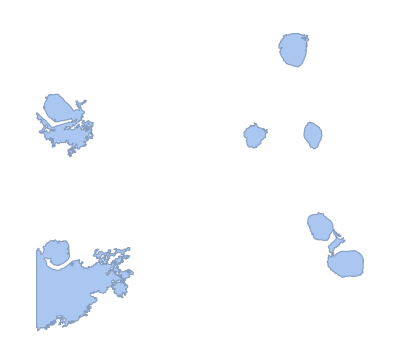

```mathematica
dmn=ImageMesh[ColorNegate@delSmall]
```

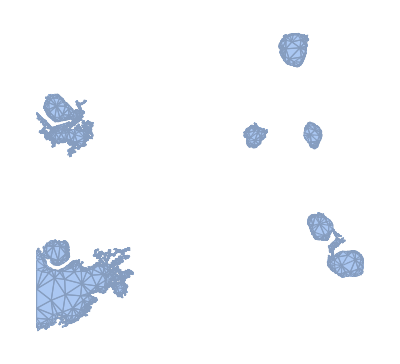

```mathematica
triann=TriangulateMesh[dmn]
```

```mathematica
Export["triangular_inv_mesh.stl",triann,"STL"]
```

triangular_inv_mesh.stl

```mathematica
MeshRegionQ[triann]
```

True

```mathematica
reg=RegionPlot[triann]
```

-Graphics-